N = 1500, d = 55, p = 55, Effective gamma = 2.01667

1. Generating XX^* and YY^* and computing Jury product...

2. Generating Marchenko-Pastur (B) and computing D U B U^*...

3. Generating Comparison Plots...

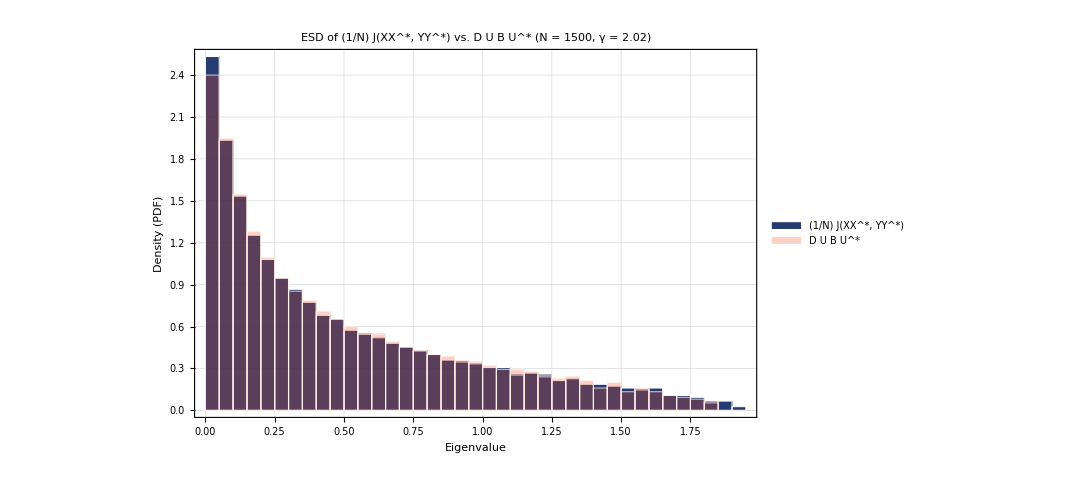

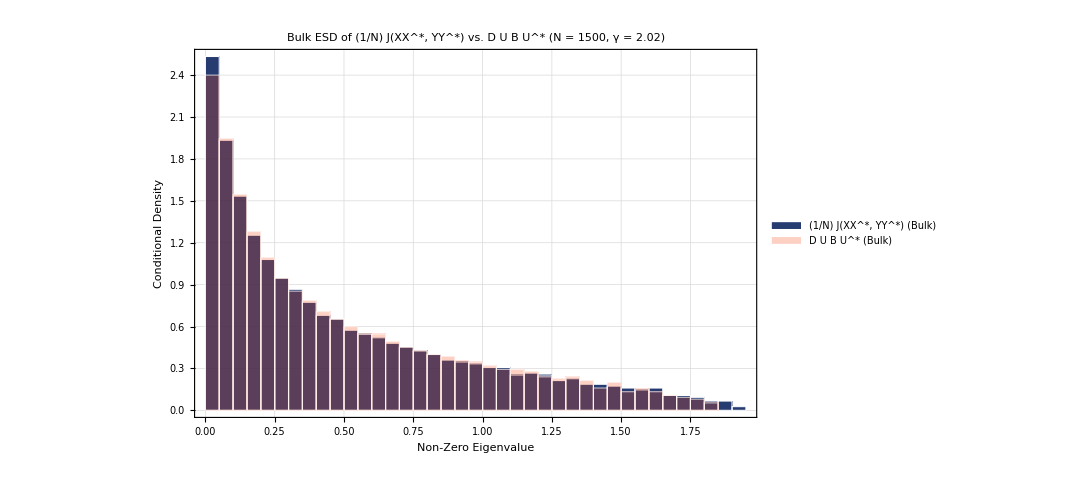

```mathematica
ClearAll["Global`*"];

(* 1. Generate normalized Complex Wishart matrix: (1/(2m)) X X^* *)
GenerateComplexWishart[n_, m_] := Module[{X, W},
  X = RandomVariate[NormalDistribution[0, 1], {n, m}] + 
      I * RandomVariate[NormalDistribution[0, 1], {n, m}];
  W = (1.0 / (2 * m)) * (X . ConjugateTranspose[X]);
  (* Force exact Hermitian structure for fast real eigensolver *)
  0.5 * (W + ConjugateTranspose[W])
]

(* 2. Define the FFT Jury Product (2D truncated convolution) *)
JuryProductFFT[A_, B_] := ListConvolve[A, B, {1, 1}, 0]

(* 3. Generate Free Poisson (Marchenko-Pastur) eigenvalues *)
GenerateFreePoisson[lambda_, alpha_, n_] := Module[{m, G, W},
  m = Max[1, Round[lambda * n]];
  G = RandomVariate[NormalDistribution[0, 1], {n, m}] + 
      I * RandomVariate[NormalDistribution[0, 1], {n, m}];
  W = (alpha / (2.0 * n)) * (G . ConjugateTranspose[G]);
  W = 0.5 * (W + ConjugateTranspose[W]);
  Re[Eigenvalues[W]]
]

(* 4. Generate eigenvalues of D U B U^* (via Hermitian D^(1/2) U B U^* D^(1/2)) *)
GenerateDUBUEigenvalues[eigenB_List, distD_, n_] := Module[
  {diagD, rootD, B, U, rotatedB, freeProduct},
  
  diagD = RandomVariate[distD, n];
  rootD = DiagonalMatrix[Sqrt[diagD]];
  B = DiagonalMatrix[eigenB];
  
  (* Haar-distributed unitary matrix U *)
  U = RandomVariate[CircularUnitaryMatrixDistribution[n]];
  rotatedB = U . B . ConjugateTranspose[U];
  
  freeProduct = rootD . rotatedB . rootD;
  freeProduct = 0.5 * (freeProduct + ConjugateTranspose[freeProduct]);
  
  Re[Eigenvalues[freeProduct]]
]

(* ========================================================================= *)
(* 5. Set Dimensions and Parameters                                          *)
(* ========================================================================= *)
n = 1500; (* Adjust to 2000 as needed *)
gammaTrue = N[2];

d = Ceiling[Sqrt[n * gammaTrue]];
p = d;
gamma = N[(d * p) / n]; (* Effective ratio dp / N *)

Print["N = ", n, ", d = ", d, ", p = ", p, ", Effective gamma = ", gamma];

(* ========================================================================= *)
(* 6. Model 1: Scaled Jury Product Z = (1/N) J(XX^*, YY^* )                   *)
(* ========================================================================= *)
Print["1. Generating XX^* and YY^* and computing Jury product..."];
XXstar = GenerateComplexWishart[n, d];
YYstar = GenerateComplexWishart[n, p];

Z = (1.0 / n) * JuryProductFFT[XXstar, YYstar];
Z = 0.5 * (Z + ConjugateTranspose[Z]);
evalsJury = Re[Eigenvalues[Z]];

(* ========================================================================= *)
(* 7. Model 2: Free Multiplicative Convolution D U B U^*                     *)
(* ========================================================================= *)
Print["2. Generating Marchenko-Pastur (B) and computing D U B U^*..."];
fpEigenvalues = GenerateFreePoisson[gamma, 1.0 / gamma, n];
uniformDist = UniformDistribution[{0, 1}];

evalsDUBU = GenerateDUBUEigenvalues[fpEigenvalues, uniformDist, n];

(* ========================================================================= *)
(* 8. Plot Comparison Histograms (UF Colors & Beamer Styled)                 *)
(* ========================================================================= *)
Print["3. Generating Comparison Plots..."];

(* University of Florida Palette *)
ufDarkNavy = RGBColor["#001A57"]; (* Deep Navy UF Blue; use "#0021A5" for classic UF Blue *)
ufOrange   = RGBColor["#FA4616"]; (* Official UF Orange *)

(* Styled Mathematical Labels for Header and Legends *)
juryLabel = Row[{"(1/N) J(X", Superscript["X", "*"], ", Y", Superscript["Y", "*"], ")"}];
dubuLabel = Row[{"D U B ", Superscript["U", "*"]}];

(* Plot A: Full Empirical Spectral Distribution *)
plotFull = Histogram[
  {evalsJury, evalsDUBU}, 
  {0.05}, 
  "PDF",
  ChartStyle -> {
    Directive[ufDarkNavy, Opacity[0.85], EdgeForm[White]],
    Directive[ufOrange, Opacity[0.25], EdgeForm[White]]
  },
  ChartLegends -> Placed[
    {juryLabel, dubuLabel}, 
    {0.72, 0.78}
  ],
  BaseStyle -> {FontSize -> 18, FontFamily -> "Helvetica"},
  Frame -> True,
  FrameLabel -> {"Eigenvalue", "Density (PDF)"},
  PlotLabel -> Style[
    Row[{
      "ESD of ", juryLabel, " vs. ", dubuLabel, 
      " (N = ", n, ", γ = ", NumberForm[gamma, {3, 2}], ")"
    }], 
    20, Bold
  ],
  GridLines -> Automatic,
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  PlotRange -> All,
  ImageSize -> 800
];

(* Plot B: Bulk Only (filtering out the (1 - gamma) Dirac delta mass at 0) *)
cutoff = 10^-6;
evalsJuryBulk = Select[evalsJury, # > cutoff &];
evalsDUBUBulk = Select[evalsDUBU, # > cutoff &];

plotBulk = Histogram[
  {evalsJuryBulk, evalsDUBUBulk}, 
  {0.05}, 
  "PDF",
  ChartStyle -> {
    Directive[ufDarkNavy, Opacity[0.85], EdgeForm[White]],
    Directive[ufOrange, Opacity[0.25], EdgeForm[White]]
  },
  ChartLegends -> Placed[
    {Row[{juryLabel, " (Bulk)"}], Row[{dubuLabel, " (Bulk)"}]}, 
    {0.72, 0.78}
  ],
  BaseStyle -> {FontSize -> 18, FontFamily -> "Helvetica"},
  Frame -> True,
  FrameLabel -> {"Non-Zero Eigenvalue", "Conditional Density"},
  PlotLabel -> Style[
    Row[{
      "Bulk ESD of ", juryLabel, " vs. ", dubuLabel, 
      " (N = ", n, ", γ = ", NumberForm[gamma, {3, 2}], ")"
    }], 
    20, Bold
  ],
  GridLines -> Automatic,
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  PlotRange -> All,
  ImageSize -> 800
];

Print[plotFull];
Print[plotBulk];
```